## Kapitola 4 - Síť RBF - aproximace na umělých datech

Demonstrace použití RBF sítě na umělých datech - aproximace funkce sinus.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Vytvoření trénovacích dat (Sin(x))

Vygenerujeme si umělá data - navzorkujeme sinusovku.

```mathematica
n=20;
x=Table[N[2π/(n-1) i],{i,0,n-1}];
y=Sin[x];
```

Takto vypadají naše data :

```mathematica
x
```

{0.,0.330694,0.661388,0.992082,1.32278,1.65347,1.98416,2.31486,2.64555,2.97625,3.30694,3.63763,3.96833,4.29902,4.62972,4.96041,5.2911,5.6218,5.95249,6.28319}

```mathematica
y
```

{0.,0.324699,0.614213,0.837166,0.9694,0.996584,0.915773,0.735724,0.475947,0.164595,-0.164595,-0.475947,-0.735724,-0.915773,-0.996584,-0.9694,-0.837166,-0.614213,-0.324699,-2.44929×10^-16}

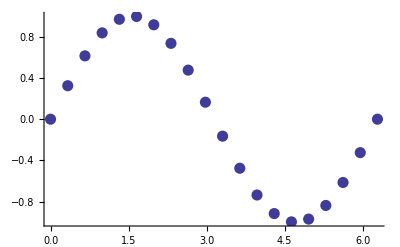

```mathematica
ListPlot[Transpose[{x,y}],PlotStyle->PointSize[0.02]]
```

## Zpracování dat neuronovou sítí

Inicializace sítě - zadáme trénovací množinu, rozdělenou na vstupní a výstupní data, a počet neuronů. Počet neuronů se zadává jako kladné celé číslo.

Vytvořenou síť si uložíme do proměnné "net".

```mathematica
net=InitializeRBFNet[x,y,5,RandomInitialization->True]
```

RBFNet[{{w1, λ, w2}, χ},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 4, 5, 13, 23, 4.0582476}, OutputNonlinearity → None, NumberOfInputs → 1}]

Můžeme si nechat zobrazit nějaké další informace o vytvořené síti.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-4-5 at 13:23. The network has 1 input and 1 output.  It consists of 5 basis functions of Exp type. The network has a linear submodel.

Podíváme se jak naše, zatím náhodně inicializovaná, síť odpovídá na data.

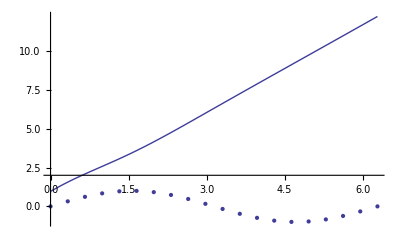

```mathematica
NetPlot[net,x,y]
```

Teď síť natrénujeme pomocí funkce "NeuralFit", které zadáme naší síť (proměnná "net"), trénovací množinu ("x" a "y") a počet učících kroků.

Funkce NeuralFit vyprodukuje naučenou síť a záznam o průběhu učení (může se hodit) - obě tyto návratové hodnoty si ukládáme (do proměnnée "net2" a "record"). Parametr "5" znamená počet prováděných iterací.

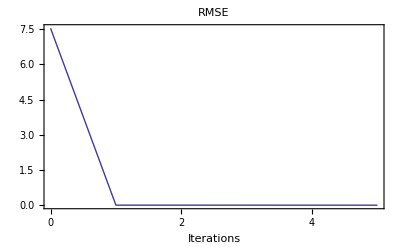

```mathematica
{net2,record}=NeuralFit[net,x,y,5];
```

Jak teď odpovídá natrénovaná síť (reprezentováno čarou) na data (body) :

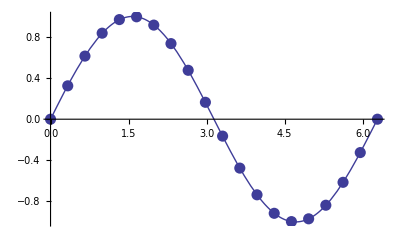

```mathematica
NetPlot[net2,x,y,PlotStyle->PointSize[0.02]]
```

Podíváme se i mimo trénovaný interval :

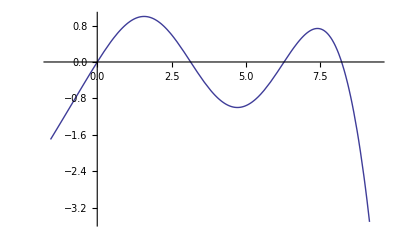

```mathematica
Plot[net2[{x}],{x,-π/2,3π}]
```

Můžeme se podívat na odpověď sítě na tzv. "data/model" diagramu - ideálně by měl být reprezentován čarou odpovídající ose 1. a 3. kvadrantu.

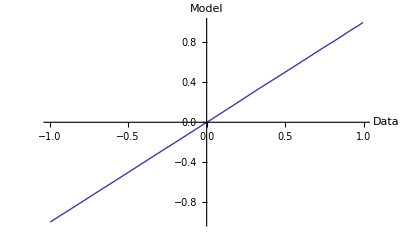

```mathematica
NetPlot[net2,x,y,DataFormat->NetOutput]
```

Takto potom vypadá síť, když ji převedeme do vzorce - určitě poznáváte aktivační funkce neuronu.

```mathematica
net2[{vstup}][[1]]
```

-7545.26-1805.57 ⅇ^(-0.0038364 (-0.775349+vstup)^2)+33.1932 ⅇ^(-0.0519129 (-0.675882+vstup)^2)+9318.26 ⅇ^(-0.000632856 (-0.44272+vstup)^2)-0.156204 ⅇ^(-0.454996 (-0.0464258+vstup)^2)-2.69356 ⅇ^(-0.166904 (0.0131257+vstup)^2)+4.25216 vstup

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.